## BudBurst

```mathematica
raw2017=Import["/Users/katjad/Documents/CitizenScienceData/CitizenScienceData/BudBurst/budburst_2017.csv"]//Rest;
raw2018=Import["/Users/katjad/Documents/CitizenScienceData/CitizenScienceData/BudBurst/budburst_2018.csv"]//Rest;
raw2019=Import["/Users/katjad/Documents/CitizenScienceData/CitizenScienceData/BudBurst/budburst_2019.csv"]//Rest;
raw2020=Import["/Users/katjad/Documents/CitizenScienceData/CitizenScienceData/BudBurst/budburst_2020.csv"]//Rest;
```

```mathematica
raw2017Association=KeyMap[DateObject[{#,{"Month","/","Day","/","Year"}}]&,Map[Length,GroupBy[raw2017,#[[28]]&]]];
raw2018Association=KeyMap[DateObject[{#,{"Month","/","Day","/","Year"}}]&,Map[Length,GroupBy[raw2018,#[[28]]&]]];
raw2019Association=KeyMap[DateObject[{#,{"Month","/","Day","/","Year"}}]&,Map[Length,GroupBy[raw2019,#[[28]]&]]];
raw2020Association=KeyMap[DateObject[{#,{"Month","/","Day","/","Year"}}]&,Map[Length,GroupBy[raw2020,#[[28]]&]]];
```

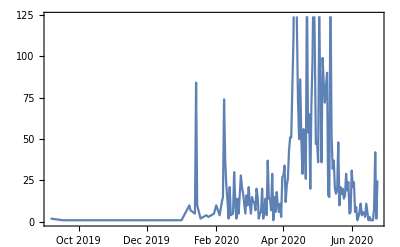

```mathematica
DateListPlot[raw2020Association]
```

```mathematica
rawAssociation=Merge[{raw2017Association,raw2018Association,raw2019Association,raw2020Association},Total];
```

```mathematica
budBurstTimeSeries=TimeSeries[rawAssociation];
```

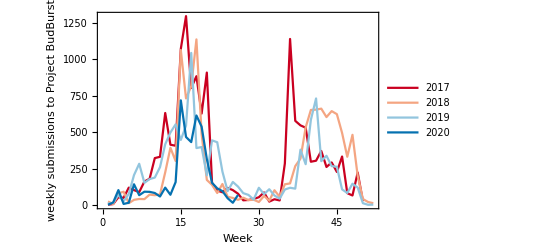

```mathematica
ListLinePlot[Lookup[#,Range[1,52]]&/@Lookup[Map[Total,GroupBy[(DateValue[#[[1]],"Week"]&)->Last]/@GroupBy[Normal[budBurstTimeSeries],DateValue[#[[1]],"Year"]&],{2}],Range[2017,2020],<||>],Frame->True,FrameLabel->{"Week","weekly submissions to Project BudBurst"},PlotLegends->{"2017","2018","2019","2020"},PlotTheme->{"LargeLabels"},PlotStyle->ResourceFunction["ColorBrewerData"]["RdBu",4]]
```

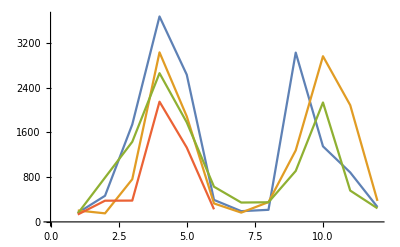

```mathematica
ListLinePlot[Lookup[#,Range[1,12]]&/@Lookup[Map[Total,GroupBy[(DateValue[#[[1]],"Month"]&)->Last]/@GroupBy[Normal[budBurstTimeSeries],DateValue[#[[1]],"Year"]&],{2}],Range[2017,2020],<||>]]
```

```mathematica
ListLinePlot[Lookup[#,Range[1,52],0]&/@Lookup[Map[Total,GroupBy[(DateValue[#[[1]],"Week"]&)->Last]/@GroupBy[Normal[budBurstTimeSeries],DateValue[#[[1]],"Year"]&],{2}],Range[2017,2020],<||>]]
```

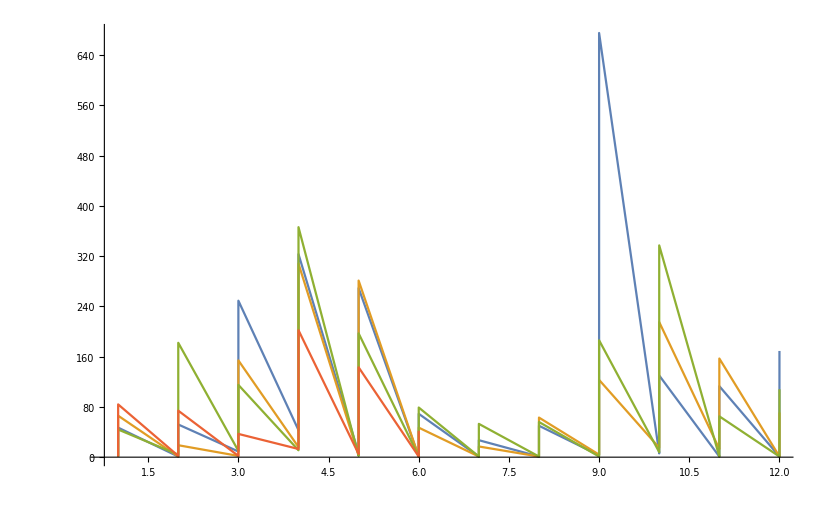

```mathematica
ListLinePlot[Values[SortBy[First]/@MapAt[DateValue[#,"Month"]&,GroupBy[Normal[budBurstTimeSeries],DateValue[#[[1]],"Year"]&],{All,All,1}]],PlotRange->All]
```

```mathematica
Grid[MapIndexed[List,raw2017[[1]]]]
```

report_id | {1}
report_type | {2}
site_species_id | {3}
species_id | {4}
common_name | {5}
family | {6}
genus | {7}
species | {8}
infra_rank | {9}
infra_epithet | {10}
sec_infra_rank | {11}
sec_infra_epithet | {12}
cultivar | {13}
plant_group_id | {14}
official_budburst_species | {15}
location_id | {16}
location_title | {17}
latitude | {18}
longitude | {19}
google_place_id | {20}
formatted_address | {21}
locality | {22}
administrative_area_level_1 | {23}
postal_code | {24}
administrative_area_level_2 | {25}
country | {26}
observation_id | {27}
observation_date | {28}
phenophase_id | {29}
phenophase_code | {30}
phenophase_plant_structure | {31}
phenophase_stage | {32}
nativars_time_start | {33}
nativars_time_end | {34}
nativars_temperature_fahrenheit | {35}
nativars_cloud_cover_id | {36}
nativars_flowering_stage_id | {37}
nativars_number_open_flowers | {38}
nativars_plant_height | {39}
ants | {40}
bees_general | {41}
bees_other | {42}
beetles | {43}
birds | {44}
bumble_bees | {45}
butterflies | {46}
butterflies_moths | {47}
carpenter_bees | {48}
flies | {49}
honey_bees | {50}
large_bees_wasps | {51}
metallic_green_bees | {52}
moths | {53}
not_sure | {54}
small_bees_flies | {55}
wasps | {56}
comments | {57}